# Modelo de irradiación solar

## Constantes

```mathematica
SOLAR=1360;
DiasJulianos=List[17,47,75,105,135,162,198,228,258,288,318,344];
Hs=List[7.689,6.804,5.714,4.238,3.323,2.821,2.989,3.805,5.167,6.224,7.244,7.541];
MesLabels ={"Enero", "Febrero", "Marzo", "Abril", "Mayo", "Junio", "Julio", "Agosto", "Septiembre", "Octubre", "Noviembre", "Diciembre"};
```

## Parámetros que ingresa el usuario

```mathematica
latitud=-31.4°; (* ϕ *)
inclinacion=latitud; (* β *)
acimut=Pi; (* γ *)
```

## Cambian a lo largo del año

```mathematica
declinacion=(23.45*Pi/180)*Sin[2*Pi*(284+n)/365]; (* δ *)
excentricidad = 1+0.033Cos[2*Pi*n/365];
anguloSalida=ArcCos[-Tan[latitud]Tan[declinacion]];
horaSalida = anguloSalida/Pi * 12;
```

```mathematica
Plot[{excentricidad, declinacion, anguloSalida},{n, 1, 365},
PlotLabel->"Valores dependientes de la epoca del año",
PlotLabels->{"Excentricidad", "Declinación", "Ángulo horario al amanecer"}
]
```

-Graphics-

## Ángulos del sol durante el día

```mathematica
anguloSolar=(h-12)Pi/12;  (* ω *)
cenit=ArcCos[ Cos[latitud]Cos[declinacion]Cos[anguloSolar]+Sin[latitud]Sin[declinacion]];
acimutSolar=If[anguloSolar<0,-1,1]Abs[ArcCos[(Cos[cenit]Sin[latitud]-Sin[declinacion])/(Sin[cenit]Cos[latitud])]];
incidencia=ArcCos[Cos[cenit]Cos[inclinacion]+Sin[cenit]Sin[inclinacion]Cos[acimutSolar-acimut]];
```

```mathematica
Manipulate[
Block[{n=DiasJulianos[[mes]], H=Hs[[mes]]},
Plot[{anguloSolar,cenit,Cos[cenit],acimutSolar,incidencia},{h,0, 24},
PlotLabel->"Ángulos solares durante 24 horas",
PlotLabels-> {"Ángulo horario", "Ángulo cenital", "Coseno del ángulo cenital", "Ángulo acimutal", "Ángulo de incidencia con el panel"},
PlotHighlighting->"XSlice"
]
],
{mes, 1, 12,1}
]
```

## Valores de irradiación

```mathematica
HoJ=(24*3600/Pi)*SOLAR*excentricidad(Cos[latitud]*Cos[declinacion]*Sin[anguloSalida]+anguloSalida*Sin[latitud]Sin[declinacion]);
Ho=HoJ/3600000;

angulo1=anguloSolar-Pi/24;angulo2=anguloSolar+Pi/24;
IoJ=(12*3600/Pi)*SOLAR*excentricidad(Cos[latitud]Cos[declinacion](Sin[angulo2]-Sin[angulo1])+(angulo2-angulo1)Sin[latitud]Sin[declinacion]);
Io=IoJ/3600000;

a=0.409+0.5016Sin[anguloSalida-Pi/3]; b=0.6609-0.4767Sin[anguloSalida-Pi/3];
rt=Pi/24*(a+b*Cos[anguloSolar])*(Cos[anguloSolar]-Cos[anguloSalida])/(Sin[anguloSalida]-anguloSalida*Cos[anguloSalida]);
II=H*rt;
kT=II/Io;
Id =II*Which[kT<=0.22,1-0.09kT,kT<=0.80,0.9511-0.1604kT+4.388kT^2-16.638kT^3+12.336kT^4,True,0.165];
Ib=II-Id;
Rb=Cos[incidencia]/Cos[cenit];
Ibn =Ib/Cos[cenit];
IT=Ib*Rb+Id*(1+Cos[inclinacion])/2;
(* Difusa de la guía *)
KT=H/Ho;
fDm=1-1.13KT;
Hd=fDm*H;
```

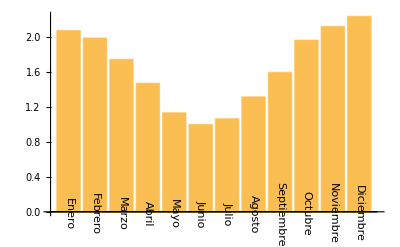

```mathematica
Manipulate[
Block[{n=DiasJulianos[[mes]], H=Hs[[mes]]},
Plot[{Io, II, Id, IT,Ibn},{h, 12-horaSalida,12+horaSalida},
PlotLabel->"Irradiación horaria en superficie horizontal",
PlotLegends->{"A tope de atmósfera", "En tierra", "Difusa", "Total", "I_bn del paso a paso"},
PlotHighlighting->"XSlice"
]
],
{mes, 1, 12,1}
]

BarChart[
Block[{n=#[[1]], H=#[[2]], h=12}, Hd] &/@Transpose[{DiasJulianos, Hs}],
ChartLabels->Placed[MesLabels, Axis, Rotate[#, -Pi/2]&]
]
```